0.24286

0.393226

0.31575

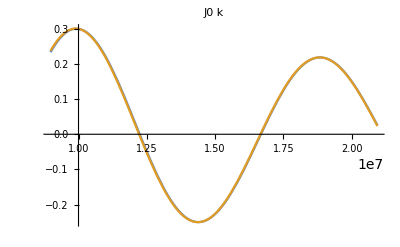

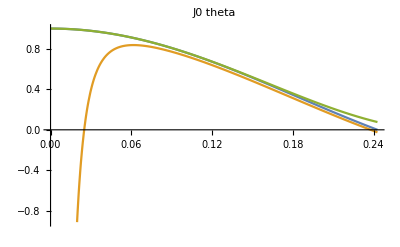

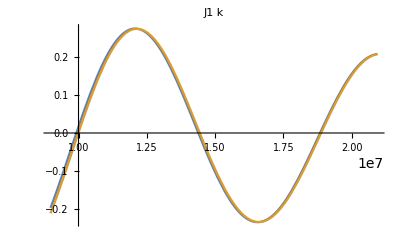

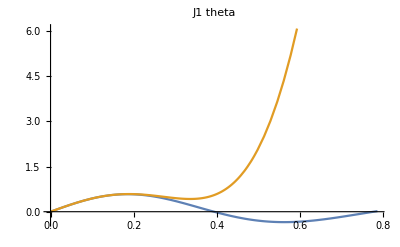

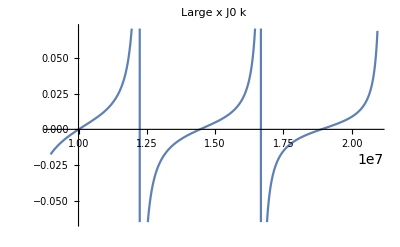

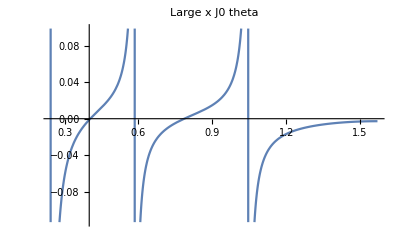

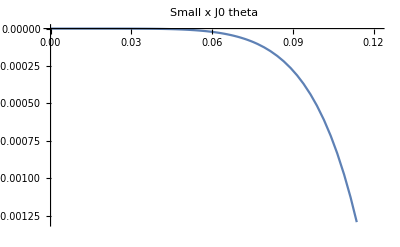

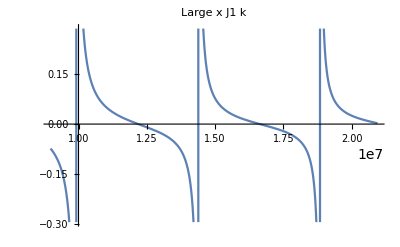

```mathematica
k=1*^7;
r=20*^-6;
a=1*^-3;
theta1=Pi/4;
zero0=ArcSin[2.4048/(a*k)]
zero1=ArcSin[3.8317/(a*k)]

Approx0[x_]:=
Sqrt[2/(Pi*x)]*(1-1/(16*x^2)(*+53/(512*x^4)*))*(Cos[x-Pi/4(*-1/(8*x)+25/(384*x^3)*)])
Approx01[x_]:=
1-2.2499997*(x/3)^2+1.2656208*(x/3)^4(*-.3163866*(x/3)^6+.0444479*(x/3)^8-.0039444*(x/3)^10+.00021(x/3)^12*)
Approx1[x_]:=
Sqrt[2/(Pi*x)]*(1+3/(16*x^2)(*-99/(512*x^4)*))*(Cos[x-3*Pi/4(*+3/(8*x)-21/(128*x^3)*)])
Approx11[x_]:=
x*(1/2-0.56249985*(x/3)^2+.21093573*(x/3)^4)(*-.03954289(x/3)^6-.00443319*(x/3)^8-.00031761*(x/3)^10+.00001109*(x/3)^12)*)

NIntegrate[Approx0[k*a*Sin[theta]]^2,{theta,zero0,Pi/2}]+NIntegrate[Approx1[k*a*Sin[theta]]^2,{theta,zero1,Pi/2}]+NIntegrate[Approx01[k*a*Sin[theta]]^2,{theta,0,zero0}]+NIntegrate[Approx11[k*a*Sin[theta]]^2,{theta,0,zero1}]

Plot[{BesselJ[0,k1*a*Sin[theta1]],Approx0[k1*a*Sin[theta1]](*,Approx01[k1*a*Sin[theta1]]}*)},{k1,(20000000 π)/7,(20000000 π)/3},PlotLabel->"J0 k"]
Plot[{BesselJ[0,k*a*Sin[theta]],Approx0[k*a*Sin[theta]],Approx01[k*a*Sin[theta]]},{theta,0,zero0},PlotLabel->"J0 theta"]

Plot[{BesselJ[1,k1*a*Sin[theta1]],Approx1[k1*a*Sin[theta1]]},(*Approx11[k1*a*Sin[theta1]]},*){k1,(20000000 π)/7,(20000000 π)/3},PlotLabel->"J1 k"]
Plot[{BesselJ[1,k*a*Sin[theta]],(*Approx1[k*a*Sin[theta]],*)Approx11[k*a*Sin[theta]]},{theta,0,2*zero1},PlotLabel->"J1 theta"]

Plot[(BesselJ[0,k1*a*Sin[theta1]]-Approx0[k1*a*Sin[theta1]])/BesselJ[0,k1*a*Sin[theta1]],{k1,(20000000 π)/7,(20000000 π)/3},PlotLabel->"Large x J0 k"]
Plot[(BesselJ[0,k*a*Sin[theta]]-Approx0[k*a*Sin[theta]])/BesselJ[0,k*a*Sin[theta]],{theta,zero0,Pi/2},PlotLabel->"Large x J0 theta"]

(*Plot[(BesselJ[0,k1*a*Sin[theta1]]-Approx01[k1*a*Sin[theta1]])/BesselJ[0,k1*a*Sin[theta1]],{k1,(20000000 π)/7,(20000000 π)/3},PlotLabel->"Small x J0 k"]*)
Plot[(BesselJ[0,k*a*Sin[theta]]-Approx01[k*a*Sin[theta]])/BesselJ[0,k*a*Sin[theta]],{theta,0,zero0/2},PlotLabel->"Small x J0 theta"]

Plot[(BesselJ[1,k1*a*Sin[theta1]]-Approx1[k1*a*Sin[theta1]])/BesselJ[1,k1*a*Sin[theta1]],{k1,(20000000 π)/7,(20000000 π)/3},PlotLabel->"Large x J1 k"]
Plot[(BesselJ[1,k*a*Sin[theta]]-Approx1[k*a*Sin[theta]])/BesselJ[1,k*a*Sin[theta]],{theta,zero1,Pi/2},PlotLabel->"Large x J1 theta"]

(*Plot[(BesselJ[1,k1*a*Sin[theta1]]-Approx11[k1*a*Sin[theta1]])/BesselJ[1,k1*a*Sin[theta1]],{k1,(20000000 π)/7,(20000000 π)/3},PlotLabel->"Small x J1 k"]*)
Plot[(BesselJ[1,k*a*Sin[theta]]-Approx11[k*a*Sin[theta]])/BesselJ[1,k*a*Sin[theta]],{theta,0,zero1/2},PlotLabel->"Small x J1 theta"]

Plot[{Approx0[k1*a*Sin[theta1]]^2,(r/a)^2*Approx1[k1*a*Sin[theta1]]^2},{k1,(20000000 π)/7,(20000000 π)/3},PlotLegends->{"Upper0","Upper1"}]

Plot[{Approx0[k*a*Sin[theta]]^2,(r/a)^2*Approx1[k*a*Sin[theta]]^2},{theta,zero1,Pi/2},PlotLegends->{"Upper0","Upper1"}]
Plot[{Approx01[k*a*Sin[theta]]^2,(r/a)^2*Approx11[k*a*Sin[theta]]^2},{theta,0,zero1},PlotLegends->{"Lower0","Lower1"}]
```